# Easing Graphs

## Wolf McNally

The Interpolate built-in easing functions, along with graphs and generated test data for comparison.

```mathematica
Linear[t_]:=t;
EaseIn[t_]:=1-Cos[t*π/2];
EaseOut[t_]:=Sin[t*π/2];
EaseInOut[t_]:=Module[{a},
a=Sin[t*π/2];
a*a
];
ExponentialIn[t_]:=2^(10*(t-1));
ExponentialOut[t_]:=-2^(-10*t)+1;
ExponentialInOut[t_]:=If[t<0.5,ExponentialIn[t*2]/2,ExponentialOut[t*2-1]/2+0.5];
BackIn[t_]:=Module[{overshoot},
overshoot=1.70158;
t*t*((overshoot+1.0)*t-overshoot)
];
BackOut[t_]:=Module[{overshoot,t2},
overshoot=1.70158;
t2=t-1;
t2*t2*((overshoot+1)*t2+overshoot)/2
];
BackInOut[t_]:=If[t<0.5,BackIn[t*2]/2,BackOut[t*2-1]+1];
BounceTime[t_]:=Module[{t2},
Which[
t<1/2.75,
	7.5625*t*t,
t<2/2.75,
	t2=t-1.5/2.75; 
	7.5625*t2*t2+0.75,
t<2.5/2.75,
	t2=t-2.25/2.75; 
	7.5625*t2*t2+0.9375,
_,
	t2=t-2.625/2.75; 
	7.5625*t2*t2+0.984375
]
];
BounceIn[t_]:=1-BounceTime[1-t];
BounceOut[t_]:=BounceTime[t];
BounceInOut[t_]:=If[t<0.5,BounceIn[t*2]/2,BounceOut[t*2-1]/2+0.5];
ElasticIn[t_]:=Module[{t2,kperiod,s},
t2=t-1;
kperiod=0.3;
s=kperiod/4;
-(2^(10*t2)*Sin[(t2-s)*2π/kperiod])
]
ElasticOut[t_]:=Module[{kperiod,s},
kperiod=0.3;
s=kperiod/4;
2^(-10*t)*Sin[(t-s)*2π/kperiod]+1
]
ElasticInOut[t_]:=If[t<0.5,ElasticIn[t*2]/2,ElasticOut[t*2-1]/2+0.5];
```

```mathematica
PlotInterpolation[f_]:=Plot[f[t],{t,0,1}, PlotRange->All];
PlotInterpolation[f_,l_]:=Show[
PlotInterpolation[f],
ListPlot[l, PlotRange->All]
];
```

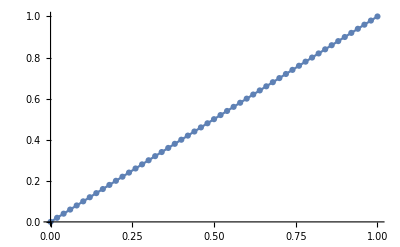

```mathematica
PlotInterpolation[Linear,{{0,0},{0.02,0.02},{0.04,0.04},{0.06,0.06},{0.08,0.08},{0.1,0.1},{0.12,0.12},{0.14,0.14},{0.16,0.16},{0.18,0.18},{0.2,0.2},{0.22,0.22},{0.24,0.24},{0.26,0.26},{0.28,0.28},{0.3,0.3},{0.32,0.32},{0.34,0.34},{0.36,0.36},{0.38,0.38},{0.4,0.4},{0.42,0.42},{0.44,0.44},{0.46,0.46},{0.48,0.48},{0.5,0.5},{0.52,0.52},{0.54,0.54},{0.56,0.56},{0.58,0.58},{0.6,0.6},{0.62,0.62},{0.64,0.64},{0.66,0.66},{0.68,0.68},{0.7,0.7},{0.72,0.72},{0.74,0.74},{0.76,0.76},{0.78,0.78},{0.8,0.8},{0.82,0.82},{0.84,0.84},{0.86,0.86},{0.88,0.88},{0.9,0.9},{0.92,0.92},{0.94,0.94},{0.96,0.96},{0.98,0.98},{1,1}}]
```

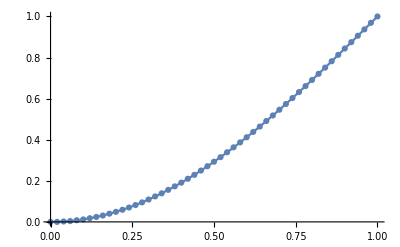

```mathematica
PlotInterpolation[EaseIn, {{0,0},{0.02,0},{0.04,0.002},{0.06,0.004},{0.08,0.008},{0.1,0.012},{0.12,0.018},{0.14,0.024},{0.16,0.031},{0.18,0.04},{0.2,0.049},{0.22,0.059},{0.24,0.07},{0.26,0.082},{0.28,0.095},{0.3,0.109},{0.32,0.124},{0.34,0.139},{0.36,0.156},{0.38,0.173},{0.4,0.191},{0.42,0.21},{0.44,0.229},{0.46,0.25},{0.48,0.271},{0.5,0.293},{0.52,0.315},{0.54,0.339},{0.56,0.363},{0.58,0.387},{0.6,0.412},{0.62,0.438},{0.64,0.464},{0.66,0.491},{0.68,0.518},{0.7,0.546},{0.72,0.574},{0.74,0.603},{0.76,0.632},{0.78,0.661},{0.8,0.691},{0.82,0.721},{0.84,0.751},{0.86,0.782},{0.88,0.813},{0.9,0.844},{0.92,0.875},{0.94,0.906},{0.96,0.937},{0.98,0.969},{1,1}}]
```

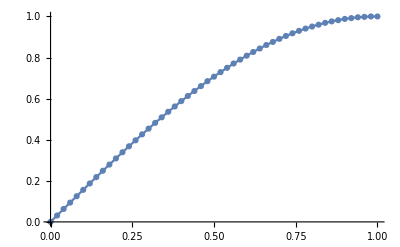

```mathematica
PlotInterpolation[EaseOut,{{0,0},{0.02,0.031},{0.04,0.063},{0.06,0.094},{0.08,0.125},{0.1,0.156},{0.12,0.187},{0.14,0.218},{0.16,0.249},{0.18,0.279},{0.2,0.309},{0.22,0.339},{0.24,0.368},{0.26,0.397},{0.28,0.426},{0.3,0.454},{0.32,0.482},{0.34,0.509},{0.36,0.536},{0.38,0.562},{0.4,0.588},{0.42,0.613},{0.44,0.637},{0.46,0.661},{0.48,0.685},{0.5,0.707},{0.52,0.729},{0.54,0.75},{0.56,0.771},{0.58,0.79},{0.6,0.809},{0.62,0.827},{0.64,0.844},{0.66,0.861},{0.68,0.876},{0.7,0.891},{0.72,0.905},{0.74,0.918},{0.76,0.93},{0.78,0.941},{0.8,0.951},{0.82,0.96},{0.84,0.969},{0.86,0.976},{0.88,0.982},{0.9,0.988},{0.92,0.992},{0.94,0.996},{0.96,0.998},{0.98,1},{1,1}}]
```

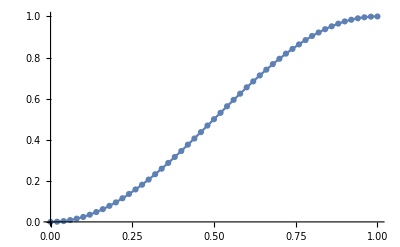

```mathematica
PlotInterpolation[EaseInOut,{{0,0},{0.02,0.001},{0.04,0.004},{0.06,0.009},{0.08,0.016},{0.1,0.024},{0.12,0.035},{0.14,0.048},{0.16,0.062},{0.18,0.078},{0.2,0.095},{0.22,0.115},{0.24,0.136},{0.26,0.158},{0.28,0.181},{0.3,0.206},{0.32,0.232},{0.34,0.259},{0.36,0.287},{0.38,0.316},{0.4,0.345},{0.42,0.376},{0.44,0.406},{0.46,0.437},{0.48,0.469},{0.5,0.5},{0.52,0.531},{0.54,0.563},{0.56,0.594},{0.58,0.624},{0.6,0.655},{0.62,0.684},{0.64,0.713},{0.66,0.741},{0.68,0.768},{0.7,0.794},{0.72,0.819},{0.74,0.842},{0.76,0.864},{0.78,0.885},{0.8,0.905},{0.82,0.922},{0.84,0.938},{0.86,0.952},{0.88,0.965},{0.9,0.976},{0.92,0.984},{0.94,0.991},{0.96,0.996},{0.98,0.999},{1,1}}]
```

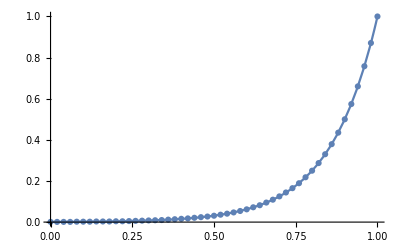

```mathematica
PlotInterpolation[ExponentialIn,{{0,0.001},{0.02,0.001},{0.04,0.001},{0.06,0.001},{0.08,0.002},{0.1,0.002},{0.12,0.002},{0.14,0.003},{0.16,0.003},{0.18,0.003},{0.2,0.004},{0.22,0.004},{0.24,0.005},{0.26,0.006},{0.28,0.007},{0.3,0.008},{0.32,0.009},{0.34,0.01},{0.36,0.012},{0.38,0.014},{0.4,0.016},{0.42,0.018},{0.44,0.021},{0.46,0.024},{0.48,0.027},{0.5,0.031},{0.52,0.036},{0.54,0.041},{0.56,0.047},{0.58,0.054},{0.6,0.062},{0.62,0.072},{0.64,0.082},{0.66,0.095},{0.68,0.109},{0.7,0.125},{0.72,0.144},{0.74,0.165},{0.76,0.189},{0.78,0.218},{0.8,0.25},{0.82,0.287},{0.84,0.33},{0.86,0.379},{0.88,0.435},{0.9,0.5},{0.92,0.574},{0.94,0.66},{0.96,0.758},{0.98,0.871},{1,1}}]
```

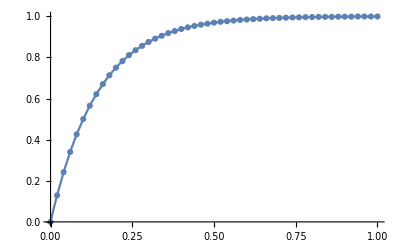

```mathematica
PlotInterpolation[ExponentialOut,{{0,0},{0.02,0.129},{0.04,0.242},{0.06,0.34},{0.08,0.426},{0.1,0.5},{0.12,0.565},{0.14,0.621},{0.16,0.67},{0.18,0.713},{0.2,0.75},{0.22,0.782},{0.24,0.811},{0.26,0.835},{0.28,0.856},{0.3,0.875},{0.32,0.891},{0.34,0.905},{0.36,0.918},{0.38,0.928},{0.4,0.938},{0.42,0.946},{0.44,0.953},{0.46,0.959},{0.48,0.964},{0.5,0.969},{0.52,0.973},{0.54,0.976},{0.56,0.979},{0.58,0.982},{0.6,0.984},{0.62,0.986},{0.64,0.988},{0.66,0.99},{0.68,0.991},{0.7,0.992},{0.72,0.993},{0.74,0.994},{0.76,0.995},{0.78,0.996},{0.8,0.996},{0.82,0.997},{0.84,0.997},{0.86,0.997},{0.88,0.998},{0.9,0.998},{0.92,0.998},{0.94,0.999},{0.96,0.999},{0.98,0.999},{1,0.999}}]
```

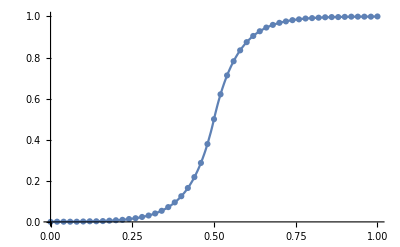

```mathematica
PlotInterpolation[ExponentialInOut,{{0,0},{0.02,0.001},{0.04,0.001},{0.06,0.001},{0.08,0.001},{0.1,0.002},{0.12,0.003},{0.14,0.003},{0.16,0.004},{0.18,0.006},{0.2,0.008},{0.22,0.01},{0.24,0.014},{0.26,0.018},{0.28,0.024},{0.3,0.031},{0.32,0.041},{0.34,0.054},{0.36,0.072},{0.38,0.095},{0.4,0.125},{0.42,0.165},{0.44,0.218},{0.46,0.287},{0.48,0.379},{0.5,0.5},{0.52,0.621},{0.54,0.713},{0.56,0.782},{0.58,0.835},{0.6,0.875},{0.62,0.905},{0.64,0.928},{0.66,0.946},{0.68,0.959},{0.7,0.969},{0.72,0.976},{0.74,0.982},{0.76,0.986},{0.78,0.99},{0.8,0.992},{0.82,0.994},{0.84,0.996},{0.86,0.997},{0.88,0.997},{0.9,0.998},{0.92,0.999},{0.94,0.999},{0.96,0.999},{0.98,0.999},{1,1}}]
```

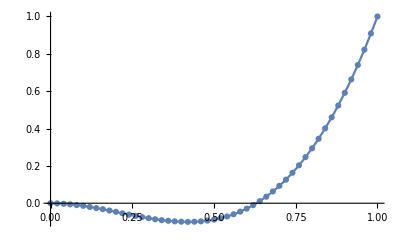

```mathematica
PlotInterpolation[BackIn,{{0,-0},{0.02,-0.001},{0.04,-0.003},{0.06,-0.006},{0.08,-0.01},{0.1,-0.014},{0.12,-0.02},{0.14,-0.026},{0.16,-0.032},{0.18,-0.039},{0.2,-0.046},{0.22,-0.054},{0.24,-0.061},{0.26,-0.068},{0.28,-0.074},{0.3,-0.08},{0.32,-0.086},{0.34,-0.091},{0.36,-0.094},{0.38,-0.097},{0.4,-0.099},{0.42,-0.1},{0.44,-0.099},{0.46,-0.097},{0.48,-0.093},{0.5,-0.088},{0.52,-0.08},{0.54,-0.071},{0.56,-0.059},{0.58,-0.045},{0.6,-0.029},{0.62,-0.01},{0.64,0.011},{0.66,0.035},{0.68,0.063},{0.7,0.093},{0.72,0.126},{0.74,0.163},{0.76,0.203},{0.78,0.247},{0.8,0.294},{0.82,0.345},{0.84,0.401},{0.86,0.46},{0.88,0.523},{0.9,0.591},{0.92,0.663},{0.94,0.74},{0.96,0.822},{0.98,0.909},{1,1}}]
```

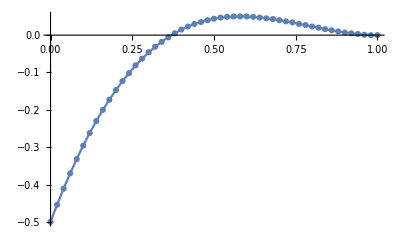

```mathematica
PlotInterpolation[BackOut,{{0,-0.5},{0.02,-0.454},{0.04,-0.411},{0.06,-0.37},{0.08,-0.332},{0.1,-0.296},{0.12,-0.262},{0.14,-0.23},{0.16,-0.2},{0.18,-0.173},{0.2,-0.147},{0.22,-0.123},{0.24,-0.102},{0.26,-0.081},{0.28,-0.063},{0.3,-0.046},{0.32,-0.031},{0.34,-0.018},{0.36,-0.006},{0.38,0.005},{0.4,0.015},{0.42,0.023},{0.44,0.03},{0.46,0.035},{0.48,0.04},{0.5,0.044},{0.52,0.047},{0.54,0.049},{0.56,0.05},{0.58,0.05},{0.6,0.05},{0.62,0.049},{0.64,0.047},{0.66,0.045},{0.68,0.043},{0.7,0.04},{0.72,0.037},{0.74,0.034},{0.76,0.03},{0.78,0.027},{0.8,0.023},{0.82,0.02},{0.84,0.016},{0.86,0.013},{0.88,0.01},{0.9,0.007},{0.92,0.005},{0.94,0.003},{0.96,0.001},{0.98,0},{1,0}}]
```

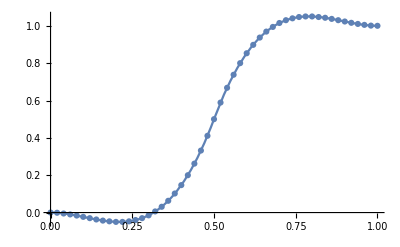

```mathematica
PlotInterpolation[BackInOut,{{0,-0},{0.02,-0.001},{0.04,-0.005},{0.06,-0.01},{0.08,-0.016},{0.1,-0.023},{0.12,-0.03},{0.14,-0.037},{0.16,-0.043},{0.18,-0.047},{0.2,-0.05},{0.22,-0.05},{0.24,-0.047},{0.26,-0.04},{0.28,-0.03},{0.3,-0.015},{0.32,0.006},{0.34,0.031},{0.36,0.063},{0.38,0.102},{0.4,0.147},{0.42,0.2},{0.44,0.262},{0.46,0.332},{0.48,0.411},{0.5,0.5},{0.52,0.589},{0.54,0.668},{0.56,0.738},{0.58,0.8},{0.6,0.853},{0.62,0.898},{0.64,0.937},{0.66,0.969},{0.68,0.994},{0.7,1.015},{0.72,1.03},{0.74,1.04},{0.76,1.047},{0.78,1.05},{0.8,1.05},{0.82,1.047},{0.84,1.043},{0.86,1.037},{0.88,1.03},{0.9,1.023},{0.92,1.016},{0.94,1.01},{0.96,1.005},{0.98,1.001},{1,1}}]
```

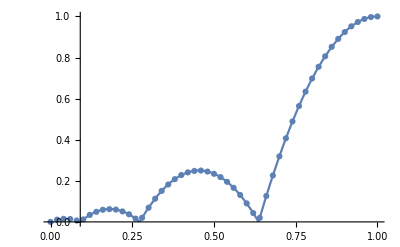

```mathematica
PlotInterpolation[BounceIn,{{0,0},{0.02,0.011},{0.04,0.015},{0.06,0.014},{0.08,0.007},{0.1,0.012},{0.12,0.034},{0.14,0.049},{0.16,0.059},{0.18,0.062},{0.2,0.06},{0.22,0.051},{0.24,0.037},{0.26,0.016},{0.28,0.02},{0.3,0.069},{0.32,0.113},{0.34,0.151},{0.36,0.182},{0.38,0.208},{0.4,0.228},{0.42,0.241},{0.44,0.248},{0.46,0.25},{0.48,0.245},{0.5,0.234},{0.52,0.218},{0.54,0.195},{0.56,0.166},{0.58,0.131},{0.6,0.09},{0.62,0.043},{0.64,0.02},{0.66,0.126},{0.68,0.226},{0.7,0.319},{0.72,0.407},{0.74,0.489},{0.76,0.564},{0.78,0.634},{0.8,0.698},{0.82,0.755},{0.84,0.806},{0.86,0.852},{0.88,0.891},{0.9,0.924},{0.92,0.952},{0.94,0.973},{0.96,0.988},{0.98,0.997},{1,1}}]
```

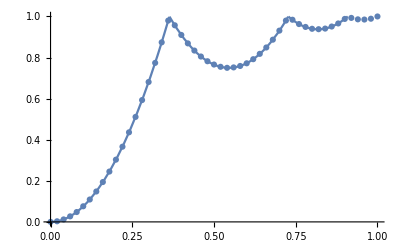

```mathematica
PlotInterpolation[BounceOut,{{0,0},{0.02,0.003},{0.04,0.012},{0.06,0.027},{0.08,0.048},{0.1,0.076},{0.12,0.109},{0.14,0.148},{0.16,0.194},{0.18,0.245},{0.2,0.303},{0.22,0.366},{0.24,0.436},{0.26,0.511},{0.28,0.593},{0.3,0.681},{0.32,0.774},{0.34,0.874},{0.36,0.98},{0.38,0.957},{0.4,0.91},{0.42,0.869},{0.44,0.834},{0.46,0.805},{0.48,0.782},{0.5,0.766},{0.52,0.755},{0.54,0.75},{0.56,0.752},{0.58,0.759},{0.6,0.772},{0.62,0.792},{0.64,0.818},{0.66,0.849},{0.68,0.887},{0.7,0.931},{0.72,0.98},{0.74,0.984},{0.76,0.963},{0.78,0.949},{0.8,0.94},{0.82,0.938},{0.84,0.941},{0.86,0.951},{0.88,0.966},{0.9,0.988},{0.92,0.993},{0.94,0.986},{0.96,0.985},{0.98,0.989},{1,1}}]
```

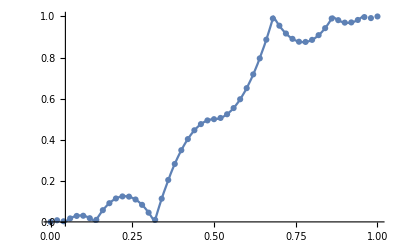

```mathematica
PlotInterpolation[BounceInOut,{{0,0},{0.02,0.008},{0.04,0.003},{0.06,0.017},{0.08,0.029},{0.1,0.03},{0.12,0.018},{0.14,0.01},{0.16,0.057},{0.18,0.091},{0.2,0.114},{0.22,0.124},{0.24,0.123},{0.26,0.109},{0.28,0.083},{0.3,0.045},{0.32,0.01},{0.34,0.113},{0.36,0.204},{0.38,0.282},{0.4,0.349},{0.42,0.403},{0.44,0.446},{0.46,0.476},{0.48,0.494},{0.5,0.5},{0.52,0.506},{0.54,0.524},{0.56,0.554},{0.58,0.597},{0.6,0.651},{0.62,0.718},{0.64,0.796},{0.66,0.887},{0.68,0.99},{0.7,0.955},{0.72,0.917},{0.74,0.891},{0.76,0.877},{0.78,0.876},{0.8,0.886},{0.82,0.909},{0.84,0.943},{0.86,0.99},{0.88,0.982},{0.9,0.97},{0.92,0.971},{0.94,0.983},{0.96,0.997},{0.98,0.992},{1,1}}]
```

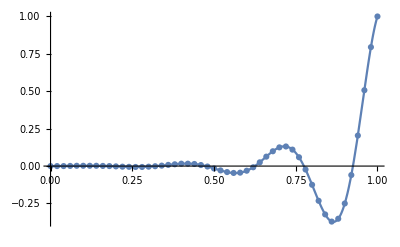

```mathematica
PlotInterpolation[ElasticIn,{{0,-0},{0.02,-0},{0.04,0},{0.06,0.001},{0.08,0.002},{0.1,0.002},{0.12,0.002},{0.14,0.002},{0.16,0.001},{0.18,-0},{0.2,-0.002},{0.22,-0.004},{0.24,-0.005},{0.26,-0.006},{0.28,-0.006},{0.3,-0.004},{0.32,-0.001},{0.34,0.003},{0.36,0.008},{0.38,0.012},{0.4,0.016},{0.42,0.016},{0.44,0.014},{0.46,0.007},{0.48,-0.003},{0.5,-0.016},{0.52,-0.029},{0.54,-0.04},{0.56,-0.046},{0.58,-0.044},{0.6,-0.031},{0.62,-0.008},{0.64,0.025},{0.66,0.063},{0.68,0.099},{0.7,0.125},{0.72,0.131},{0.74,0.11},{0.76,0.059},{0.78,-0.023},{0.8,-0.125},{0.82,-0.232},{0.84,-0.323},{0.86,-0.371},{0.88,-0.352},{0.9,-0.25},{0.92,-0.06},{0.94,0.204},{0.96,0.507},{0.98,0.795},{1,1}}]
```

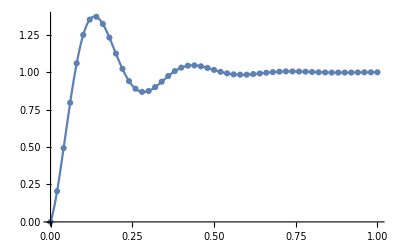

```mathematica
PlotInterpolation[ElasticOut,{{0,0},{0.02,0.205},{0.04,0.493},{0.06,0.796},{0.08,1.06},{0.1,1.25},{0.12,1.352},{0.14,1.371},{0.16,1.323},{0.18,1.232},{0.2,1.125},{0.22,1.023},{0.24,0.941},{0.26,0.89},{0.28,0.869},{0.3,0.875},{0.32,0.901},{0.34,0.937},{0.36,0.975},{0.38,1.008},{0.4,1.031},{0.42,1.044},{0.44,1.046},{0.46,1.04},{0.48,1.029},{0.5,1.016},{0.52,1.003},{0.54,0.993},{0.56,0.986},{0.58,0.984},{0.6,0.984},{0.62,0.988},{0.64,0.992},{0.66,0.997},{0.68,1.001},{0.7,1.004},{0.72,1.006},{0.74,1.006},{0.76,1.005},{0.78,1.004},{0.8,1.002},{0.82,1},{0.84,0.999},{0.86,0.998},{0.88,0.998},{0.9,0.998},{0.92,0.998},{0.94,0.999},{0.96,1},{0.98,1},{1,1}}]
```

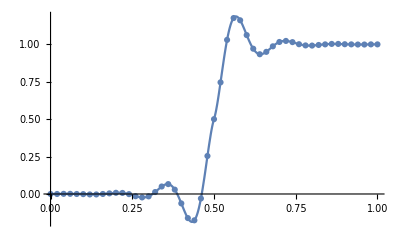

```mathematica
PlotInterpolation[ElasticInOut,{{0,-0},{0.02,0},{0.04,0.001},{0.06,0.001},{0.08,0},{0.1,-0.001},{0.12,-0.003},{0.14,-0.003},{0.16,-0},{0.18,0.004},{0.2,0.008},{0.22,0.007},{0.24,-0.001},{0.26,-0.015},{0.28,-0.023},{0.3,-0.016},{0.32,0.013},{0.34,0.05},{0.36,0.066},{0.38,0.029},{0.4,-0.063},{0.42,-0.161},{0.44,-0.176},{0.46,-0.03},{0.48,0.254},{0.5,0.5},{0.52,0.746},{0.54,1.03},{0.56,1.176},{0.58,1.161},{0.6,1.062},{0.62,0.971},{0.64,0.934},{0.66,0.95},{0.68,0.987},{0.7,1.016},{0.72,1.023},{0.74,1.015},{0.76,1.001},{0.78,0.993},{0.8,0.992},{0.82,0.996},{0.84,1},{0.86,1.003},{0.88,1.003},{0.9,1.001},{0.92,1},{0.94,0.999},{0.96,0.999},{0.98,1},{1,1}}]
```